# Mutation recurrence distribution plots

## Data import

```mathematica
path = "./results/all-projects";
```

```mathematica
project = "all"
```

all

```mathematica
chompedFiles = Table[
If[StringContainsQ[file, project<>".recurrence_distribution.tsv"],file,Nothing],
{file, StringSplit[RunProcess[{"ls", path}, "StandardOutput"]]}
]
```

{AKT1.all.recurrence_distribution.tsv,all.all.recurrence_distribution.tsv,ATM.all.recurrence_distribution.tsv,ATR.all.recurrence_distribution.tsv,BRCA1.all.recurrence_distribution.tsv,CDK2.all.recurrence_distribution.tsv,CDKN1A.all.recurrence_distribution.tsv,CHEK1.all.recurrence_distribution.tsv,CHEK2.all.recurrence_distribution.tsv,E2F1.all.recurrence_distribution.tsv,ERBB2.all.recurrence_distribution.tsv,HRAS.all.recurrence_distribution.tsv,KRAS.all.recurrence_distribution.tsv,MDM2.all.recurrence_distribution.tsv,NRAS.all.recurrence_distribution.tsv,RAF1.all.recurrence_distribution.tsv,RB1.all.recurrence_distribution.tsv,TP53.all.recurrence_distribution.tsv}

```mathematica
filename = StringReplace["path/file", {"path" -> path, "file" -> #}] &
```

StringReplace[path/file,{path→path,file→#1}]&

```mathematica
data = Table[
{
file,
Import[filename[file], "Table"]
},
{file, chompedFiles}
];
data[[1]]
```

{AKT1.all.recurrence_distribution.tsv,{{#,Project:,All,Gene:,AKT1(ENSG00000142208),Tested,donors:,10648},{MUTATIONS,AFFECTED_DONORS_PER_MUTATION},{291,1},{7,2},{2,3},{2,4},{2,6},{1,35}}}

```mathematica
GetDistribution = Reverse[
#[[2,3;;]],
{2}
]&
```

Reverse[#1⟦2,3;;All⟧,{2}]&

```mathematica
#[[2,3;;]]&[data[[1]]]
```

{{291,1},{7,2},{2,3},{2,4},{2,6},{1,35}}

```mathematica
GetLoweredDistribution=
Map[
{#[[2]], #[[1]]-1}&,
#[[2,3;;]]& [#]
]&
```

({#1⟦2⟧,#1⟦1⟧-1}&)/@(#1⟦2,3;;All⟧&)[#1]&

```mathematica
GetLabel = "Gene:"<>#[[2,1,5]]&
```

Gene:<>#1⟦2,1,5⟧&

```mathematica
GetSimpleLabel = "Gene:"<>StringSplit[#[[2,1,5]], "("][[1]]&
```

Gene:<>StringSplit[#1⟦2,1,5⟧,(]⟦1⟧&

```mathematica
GetLabeledDistribution = Labeled[GetLabel[#], GetDistribution[#]]&
```

GetLabel[#1]GetDistribution[#1]&

```mathematica
GetLoweredLabeledDistribution = Labeled[GetLabel[#], GetLoweredDistribution[#]]&
```

GetLabel[#1]GetLoweredDistribution[#1]&

```mathematica
GetAxesLabels = Reverse[#[[2,2]]&[ #[[1]]] ]&
```

Reverse[(#1⟦2,2⟧&)[#1⟦1⟧]]&

```mathematica
GetLabel /@ data
```

{Gene:AKT1(ENSG00000142208),Gene:All,Gene:ATM(ENSG00000149311),Gene:ATR(ENSG00000175054),Gene:BRCA1(ENSG00000012048),Gene:CDK2(ENSG00000123374),Gene:CDKN1A(ENSG00000124762),Gene:CHEK1(ENSG00000149554),Gene:CHEK2(ENSG00000183765),Gene:E2F1(ENSG00000101412),Gene:ERBB2(ENSG00000141736),Gene:HRAS(ENSG00000174775),Gene:KRAS(ENSG00000133703),Gene:MDM2(ENSG00000135679),Gene:NRAS(ENSG00000213281),Gene:RAF1(ENSG00000132155),Gene:RB1(ENSG00000139687),Gene:TP53(ENSG00000141510)}

```mathematica
GetSimpleLabel /@ data
```

{Gene:AKT1,Gene:All,Gene:ATM,Gene:ATR,Gene:BRCA1,Gene:CDK2,Gene:CDKN1A,Gene:CHEK1,Gene:CHEK2,Gene:E2F1,Gene:ERBB2,Gene:HRAS,Gene:KRAS,Gene:MDM2,Gene:NRAS,Gene:RAF1,Gene:RB1,Gene:TP53}

```mathematica
labeledDistributions=Map[Labeled[GetLoweredDistribution[#],GetSimpleLabel[#]]&, data];
```

```mathematica
legendedDistributions=Map[Legended[GetLoweredDistribution[#],GetSimpleLabel[#]]&, data];
```

```mathematica
rawDistributions=GetDistribution/@ data;
```

```mathematica
loweredDistributions = GetLoweredDistribution /@ data;
```

## Get mean values

{{1,1},{2,3},{3,5},{4,1},{5,5},{6,3},{7,2}}

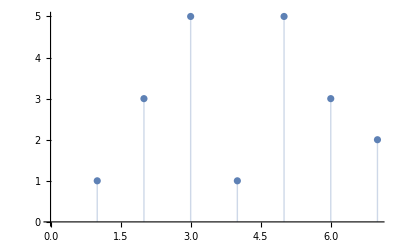

```mathematica
a={{1,1},{2,3},{3,5},{4,1},{5,5},{6,3},{7,2}}
ListPlot[a, Filling->Axis]
```

```mathematica
Times[2,3]
```

6

```mathematica
GetMean = Total[Map[(Times @@ #&),#]]/ Total[#[[All,2]]]&
```

Total[(Times@@#1&)/@#1]/Total[#1⟦All,2⟧]&

```mathematica
Map[(Times @@ #)&, a]
```

{1,6,15,4,25,18,14}

```mathematica
Total[Map[(Times @@ #)&, a]]
```

83

```mathematica
Total[a[[All,2]]]
```

20

```mathematica
GetMean[a]
```

83/20

```mathematica
N[GetMean @ a]
```

4.15

```mathematica
means = GetMean/@ Map[GetDistribution, data]
```

{6/5,12570715/11673293,1476/1369,1412/1305,938/885,148/147,149/139,95/92,373/309,224/215,825/706,226/167,462/145,115/107,251/109,145/137,727/682,3588/1213}

```mathematica
N /@ means
```

{1.2,1.07688,1.07816,1.08199,1.05989,1.0068,1.07194,1.03261,1.20712,1.04186,1.16856,1.35329,3.18621,1.07477,2.30275,1.05839,1.06598,2.95796}

```mathematica
MapLabels= Table[
Labeled[ #1[[i]],#2[[i]] ],
{i, Length[#1]}
] &
```

Table[#1⟦i⟧#2⟦i⟧,{i,Length[#1]}]&

```mathematica
MapLegends = Table[
Legended[ #1[[i]],#2[[i]] ],
{i, Length[#1]}
] &
```

Part::pkspec1: The expression i cannot be used as a part specification.

Table[#1⟦i⟧,{i,Length[#1]}]&

```mathematica
labeledMeans = MapLegends[ N/@means,GetSimpleLabel/@data] // TableForm
```

1.2
1.07688
1.07816
1.08199
1.05989
1.0068
1.07194
1.03261
1.20712
1.04186
1.16856
1.35329
3.18621
1.07477
2.30275
1.05839
1.06598
2.95796

```mathematica
namedMeans = Table[
{Map[GetLabel,data][[i]],N @means[[i]]},
{i, Length[means]}
] // TableForm
```

Gene:AKT1(ENSG00000142208) | 1.2
Gene:All | 1.07688
Gene:ATM(ENSG00000149311) | 1.07816
Gene:ATR(ENSG00000175054) | 1.08199
Gene:BRCA1(ENSG00000012048) | 1.05989
Gene:CDK2(ENSG00000123374) | 1.0068
Gene:CDKN1A(ENSG00000124762) | 1.07194
Gene:CHEK1(ENSG00000149554) | 1.03261
Gene:CHEK2(ENSG00000183765) | 1.20712
Gene:E2F1(ENSG00000101412) | 1.04186
Gene:ERBB2(ENSG00000141736) | 1.16856
Gene:HRAS(ENSG00000174775) | 1.35329
Gene:KRAS(ENSG00000133703) | 3.18621
Gene:MDM2(ENSG00000135679) | 1.07477
Gene:NRAS(ENSG00000213281) | 2.30275
Gene:RAF1(ENSG00000132155) | 1.05839
Gene:RB1(ENSG00000139687) | 1.06598
Gene:TP53(ENSG00000141510) | 2.95796

## Data display

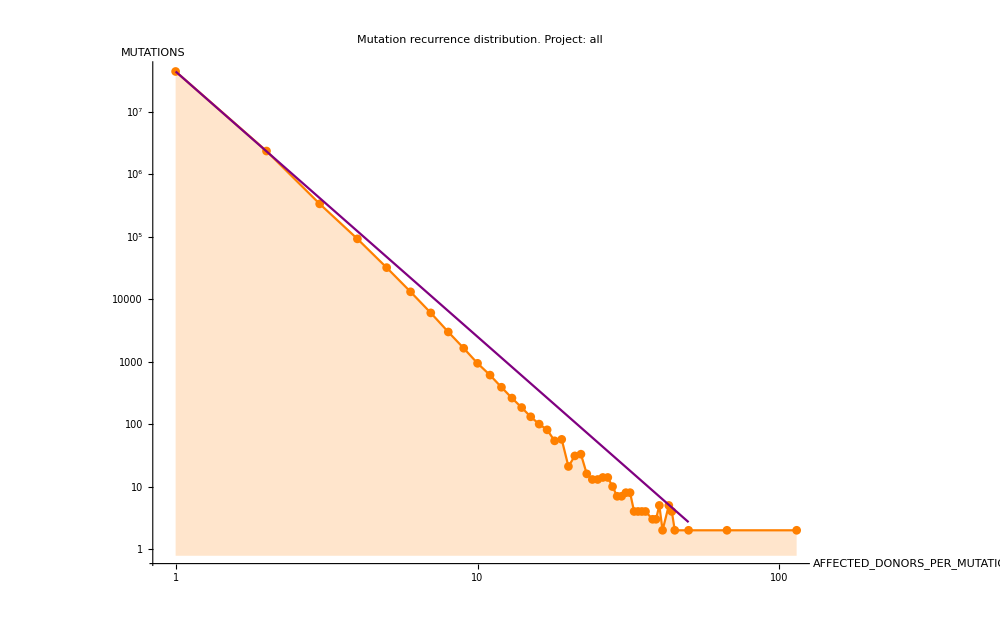

./results/all-projects/AllGenesPlot.png

```mathematica
all = rawDistributions⟦2⟧ // Select[(#⟦2⟧ > 1)&];
allFit = NonlinearModelFit[#, A x^B,{A,B},x]& [rawAll];
allPlot = Show[
ListLogLogPlot[all, 
Joined -> True, 
PlotMarkers-> Automatic, 
Filling->Bottom, 
ImageSize->1000,
AxesLabel->labels,
PlotStyle-> Orange,
PlotLabel->"Mutation recurrence distribution. Project: "<>project
],
LogLogPlot[Normal[allFit],
{x, 1, 50},
PlotStyle->Purple,
ImageSize->1000
]
]
Export[filename["AllGenesPlot.png"], allPlot]
```

```mathematica
labels = GetAxesLabels[data]
```

{AFFECTED_DONORS_PER_MUTATION,MUTATIONS}

```mathematica
logLogAllPlotsLabeled = Show[
ListLogLogPlot[#, 
Joined -> True, 
PlotMarkers-> Automatic, 
Filling->Bottom, 
ImageSize->1000,
AxesLabel->labels
]& [labeledDistributions],
PlotLabel->"Mutation recurrence distribution. Project: "<>project
]
Export[filename["logLogAllPlotsLabeled.png"], logLogAllPlotsLabeled]
```

-Graphics-

./results/all-projects/logLogAllPlotsLabeled.png

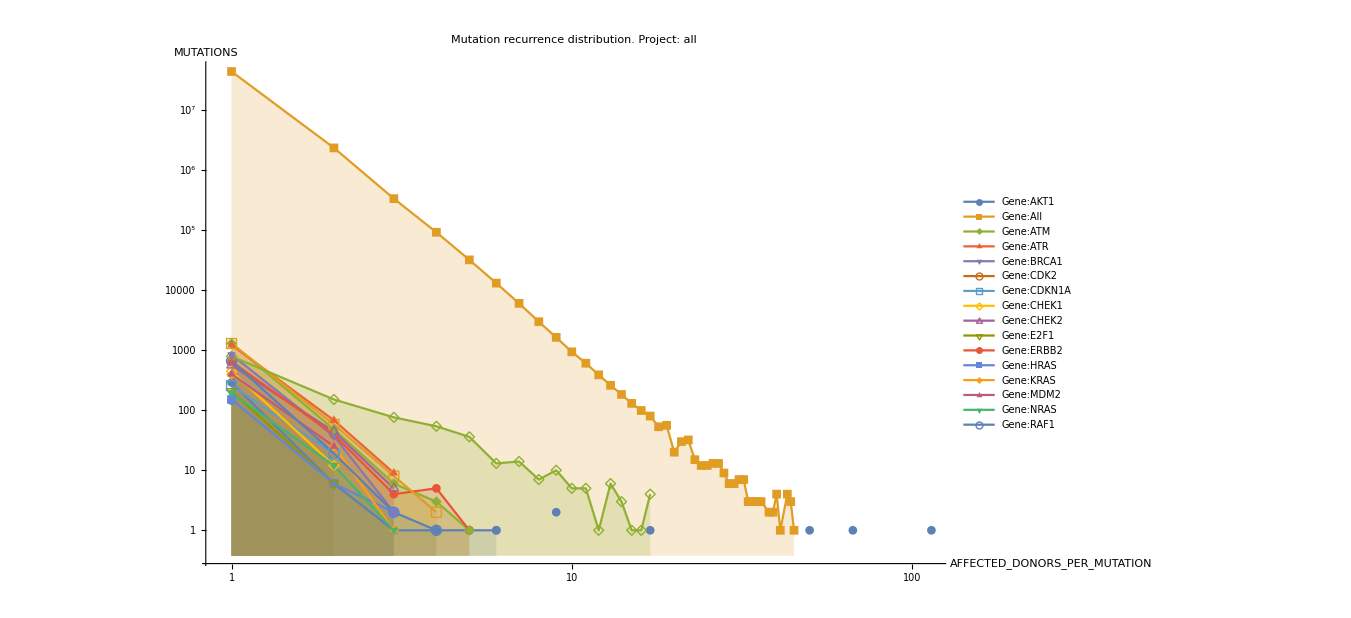

./results/all-projects/logLogAllPlotsLegended.png

```mathematica
logLogAllPlotsLegended = Show[
ListLogLogPlot[#, 
Joined -> True, 
PlotMarkers-> Automatic, 
Filling->Bottom, 
ImageSize->1000,
AxesLabel->labels
]& [legendedDistributions],
PlotLabel->"Mutation recurrence distribution. Project: "<>project
]
Export[filename["logLogAllPlotsLegended.png"], logLogAllPlotsLegended]
```

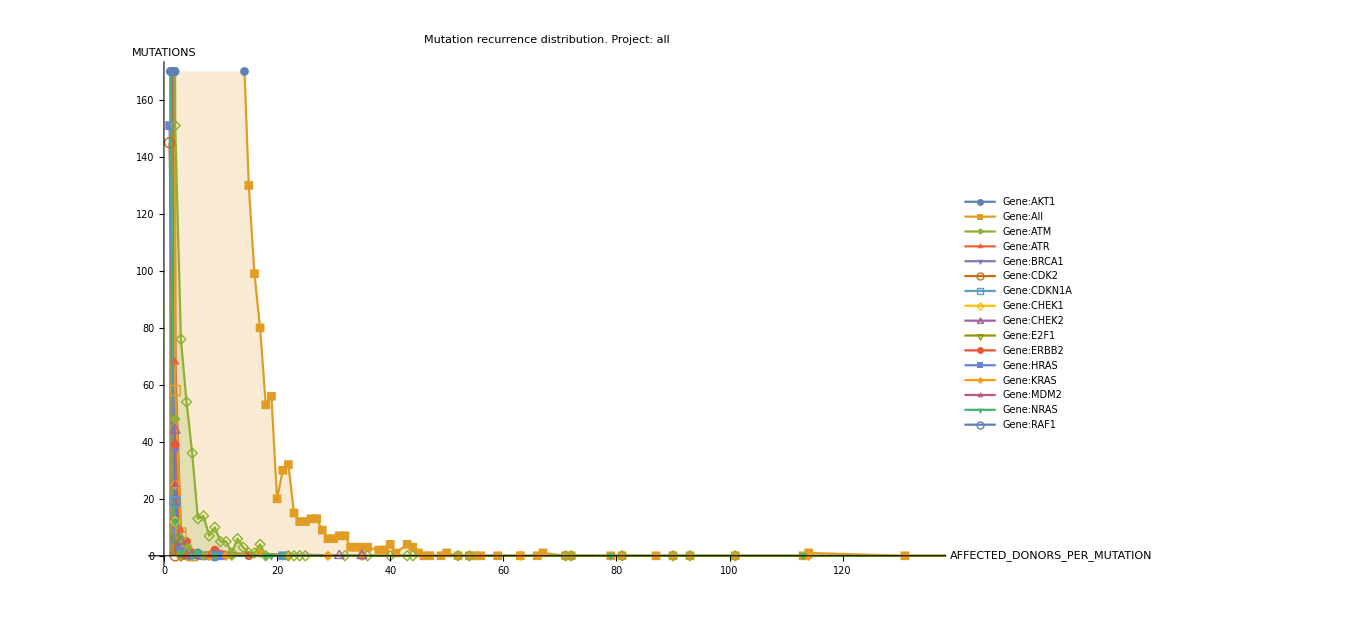

```mathematica
allPlotsLegended = Show[
ListPlot[#, 
Joined -> True, 
PlotMarkers-> Automatic, 
Filling->Bottom, 
ImageSize->1000,
AxesLabel->labels
]& [legendedDistributions],
PlotLabel->"Mutation recurrence distribution. Project: "<>project
]
```

```mathematica
LogLogPlots = Show[
ListLogLogPlot[#, 
Joined -> True, 
PlotMarkers-> Automatic, 
Filling->Bottom, 
ImageSize->500,
AxesLabel->labels
],
PlotLabel->"Mutation recurrence distribution. Project: "<>project
]& /@ labeledDistributions
LogLogPlotGrid = GraphicsGrid[Partition[LogLogPlots, UpTo[3]]];
Remove[LogLogPlots];
Export[filename["logLogPlotGrid.png"], LogLogPlotGrid]
Remove[LogLogPlotGrid];
```

First::normal: Nonatomic expression expected at position 1 in First[Automatic].

General::stop: Further output of First::normal will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

./results/all-projects/logLogPlotGrid.png

## Power law fit

```mathematica
fits=NonlinearModelFit[#, A x^B,{A,B},x]& /@ loweredDistributions
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{FittedModel[289.999/x^5.57055],FittedModel[(4.38672×10^7)/x^84.8726],FittedModel[1303./x^4.76605],FittedModel[1221.03/x^4.19506],FittedModel[841.015/x^4.5443],FittedModel[145./x^265.426],FittedModel[257./x^3.7577],FittedModel[445.003/x^5.24486],FittedModel[562.062/x^3.74328],FittedModel[206.002/x^5.13661],FittedModel[647.012/x^4.07773],FittedModel[150.997/x^4.59855],FittedModel[393.031/x^4.05192],FittedModel[399.031/x^4.0796],FittedModel[193.008/x^4.05306],FittedModel[658./x^5.11777],FittedModel[1291.01/x^4.48702],FittedModel[788.165/x^2.22513]}

```mathematica
fitParameters = MapLegends[#["ParameterTable"]& /@ fits,GetSimpleLabel/@data];
fitParameters // TableForm
```

FittedModel::dof: The number of parameters 2 is not less than the number of data values 2. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

FittedModel::dof: The number of parameters 2 is not less than the number of data values 2. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

| Estimate | Standard Error | t-Statistic | P-Value
A | 289.999 | 0.684616 | 423.594 | 1.86353×10^-10
B | -5.57055 | 0.159576 | -34.9084 | 4.01847×10^-6
 | Estimate | Standard Error | t-Statistic | P-Value
A | 4.38672×10^7 | 278933. | 157.268 | 4.29389×10^-93
B | -84.8726 | 6.76165×10^-39 | -1.25521×10^40 | 5.34909159550794×10^-2822
 | Estimate | Standard Error | t-Statistic | P-Value
A | 1303. | 0.657684 | 1981.2 | 1.11618×10^-18
B | -4.76605 | 0.0192674 | -247.364 | 2.94559×10^-13
 | Estimate | Standard Error | t-Statistic | P-Value
A | 1221.03 | 2.51411 | 485.671 | 1.07838×10^-10
B | -4.19506 | 0.0520007 | -80.6731 | 1.41512×10^-7
 | Estimate | Standard Error | t-Statistic | P-Value
A | 841.015 | 2.23983 | 375.482 | 4.16574×10^-8
B | -4.5443 | 0.0869683 | -52.2524 | 0.0000154376
Missing[]
Missing[]
 | Estimate | Standard Error | t-Statistic | P-Value
A | 445.003 | 1.42413 | 312.473 | 0.00203735
B | -5.24486 | 0.172089 | -30.4775 | 0.0208807
 | Estimate | Standard Error | t-Statistic | P-Value
A | 562.062 | 2.58567 | 217.376 | 3.90975×10^-11
B | -3.74328 | 0.0831725 | -45.0062 | 1.02246×10^-7
 | Estimate | Standard Error | t-Statistic | P-Value
A | 206.002 | 0.743686 | 277.001 | 0.00229825
B | -5.13661 | 0.179821 | -28.5652 | 0.0222775
 | Estimate | Standard Error | t-Statistic | P-Value
A | 647.012 | 1.95399 | 331.123 | 5.1204×10^-14
B | -4.07773 | 0.0699563 | -58.2896 | 1.71295×10^-9
 | Estimate | Standard Error | t-Statistic | P-Value
A | 150.997 | 0.445383 | 339.027 | 4.44469×10^-14
B | -4.59855 | 0.0998827 | -46.0395 | 7.03557×10^-9
 | Estimate | Standard Error | t-Statistic | P-Value
A | 393.031 | 1.17391 | 334.804 | 5.68424×10^-27
B | -4.05192 | 0.0679091 | -59.6668 | 3.04178×10^-17
 | Estimate | Standard Error | t-Statistic | P-Value
A | 399.031 | 3.36511 | 118.579 | 0.0000711115
B | -4.0796 | 0.196943 | -20.7146 | 0.00232236
 | Estimate | Standard Error | t-Statistic | P-Value
A | 193.008 | 0.52963 | 364.42 | 4.49084×10^-20
B | -4.05306 | 0.0628303 | -64.5081 | 2.6092×10^-13
 | Estimate | Standard Error | t-Statistic | P-Value
A | 658. | 0.342834 | 1919.3 | 3.11921×10^-10
B | -5.11777 | 0.0255677 | -200.165 | 2.74958×10^-7
 | Estimate | Standard Error | t-Statistic | P-Value
A | 1291.01 | 1.0289 | 1254.74 | 1.11637×10^-9
B | -4.48702 | 0.0248885 | -180.285 | 3.7631×10^-7
 | Estimate | Standard Error | t-Statistic | P-Value
A | 788.165 | 5.27938 | 149.291 | 1.73795×10^-49
B | -2.22513 | 0.0343227 | -64.8297 | 3.23593×10^-37

```mathematica
fitFunctions = Normal[#]& /@ fits;
MapLegends[fitFunctions,GetSimpleLabel/@data]
```

{289.999/x^5.57055,(4.38672×10^7)/x^84.8726,1303./x^4.76605,1221.03/x^4.19506,841.015/x^4.5443,145./x^265.426,257./x^3.7577,445.003/x^5.24486,562.062/x^3.74328,206.002/x^5.13661,647.012/x^4.07773,150.997/x^4.59855,393.031/x^4.05192,399.031/x^4.0796,193.008/x^4.05306,658./x^5.11777,1291.01/x^4.48702,788.165/x^2.22513}

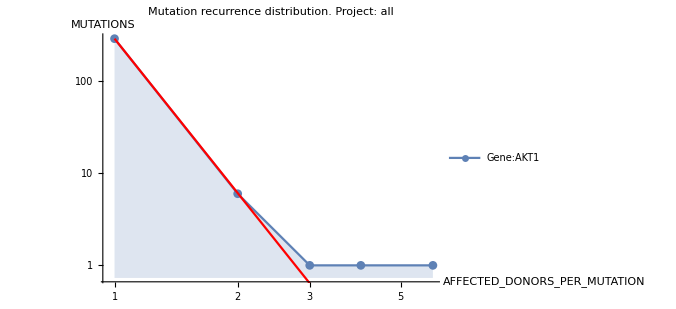
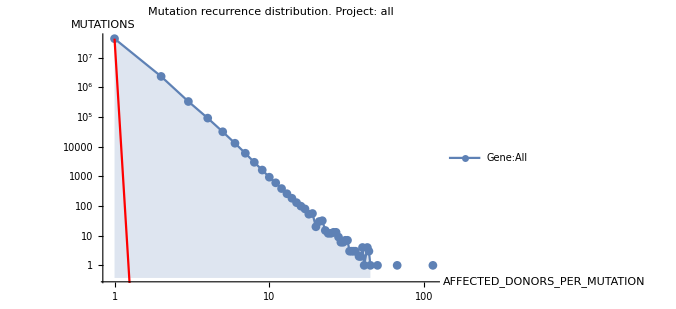
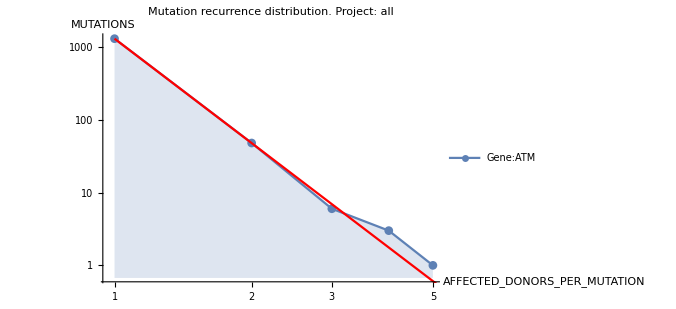
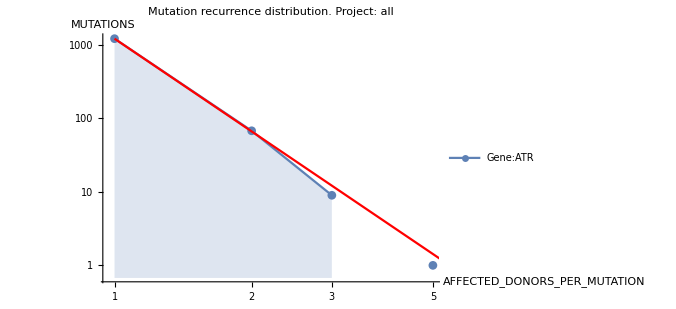
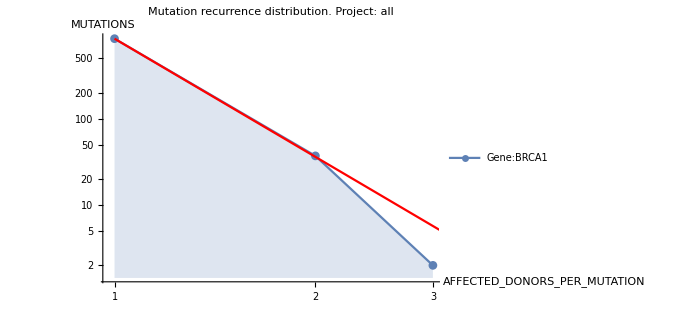
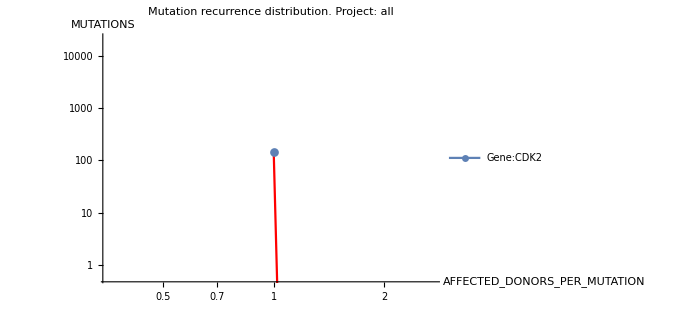
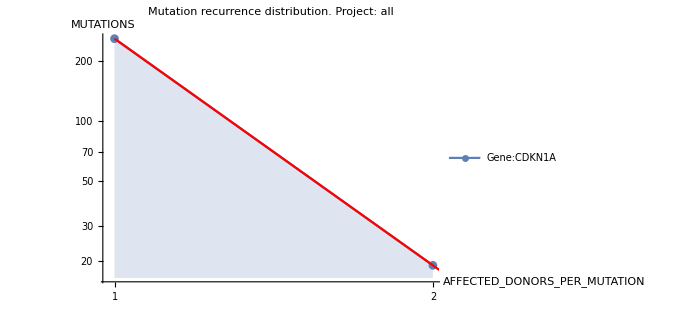
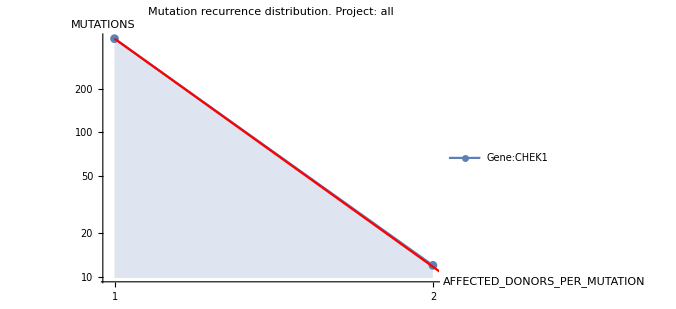

```mathematica
fitPlots = Table[
Show[
ListLogLogPlot[#1[[i]], 
Joined -> True, 
PlotMarkers-> Automatic, 
Filling->Bottom, 
AxesLabel->labels
],
LogLogPlot[
#2[[i]][x],{x,1,50}, PlotStyle->Red
],
ImageSize->500,
PlotLabel->"Mutation recurrence distribution. Project: "<>project
],
{i,Length[#1]}
]&[legendedDistributions, fits]
(*GraphicsGrid[Partition[fitPlots, 2], ImageSize->{1500,Automatic }]*)
```